Genez, Inc.
9617 Black Watch Court
Charlotte, NC 28277

February 18, 2020

To: Chief Scientist, Center for Bioinformatics
From: Aakriti Lakshmanan
Subj: Analysis of Mouse Data

## Summary and Introduction

### Abstract:

As requested in the Scope of Work, we have conducted an analysis on the differences between the A/J strain and the C57BL/6 strain. This analysis included an indepth review of a study conducted on the impact of radiation on these two strains.

### Introduction/Background Information:

Animal models are an integral part of scientific discovery. They allow scientists to model and test out treatments, in a low cost and low risk environment. Mice have always been one of the top animal models used in research. The main reason that they are so viable for use in these applications is because they are low cost, there are less ethical problems, and their genome is very similar to humans. because of this similarity, treatments and diseases can be modeled in mice to learn about how they will perform in humans. Most of the mice are albinos, due to a mutation in their tyrosinase gene. There are many different strains of mice, which all display different mutations in their genome. This allows scientists to see the effects on different populations, and study specific disease that a strain may have. These strains have a uniform genome, which is created by inbreeding the offspring for 20 generations. By this point, all the offspring have identical genomes, with the same variants and SNPs. [1]

	The most common strain is the C57BL/6 strain, otherwise known as the black 6 mice strain. This is the first mouse that had their genome sequenced. They do not form tumors that easily, and have a low bone density. They also develop hearing loss as they grow older. This strain was created by Dr. CC Little in 1921, and as time has gone on, the main strain has been split into may sub-strain that all portray a slightly different genome. They are commonly used as a control for experiments, and are also used as a background for mating with other strains due to their low number of SNPs. The following table shows the weight of this strain as it grows older. 
-Graphics-
The males of this strain tend to weigh more than the females. The coat of this mice is unusually black, ichi is due to the fact that there is no mutation on their tyrosinase gene, here the common name black 6. [2]

	One of the main qualities of this strain is hearing loss. This is regulated by the Cdh23 gene, otherwise known as the cadherin gene. In black 6 mice, there is a SNP at nucleotide 752 of Cdh23. A guanine nucleotide is swapped out for an adenine nucleotide, and causes the exon to not be produced correctly. This gene is important for the sensory perception of sound, as well as inner ear morphogenesis. The mutation in this gene impedes the gene’s ability to function as normal. It interacts with multiple different markers. This mutation is also found in multiple different strains, including the A/J strain, which will be discussed later. The following image analyzed the expression of this gene in the ear of this mice strain. 
	-Graphics-
	
	This gene is expressed through abnormal ear morphology and abnormal cochlear hair cells. In total, the combination of all these different effects leads to hair loss in the mice. [3,4] The following image shows the syteny between black mouse 6 chromosome and the human genome. 
	-Graphics-
	
	Syteny is the location of genetic loci on a chromosome. Blocks of chromosomes stay the same, and this allows scientists to map chromosomes in between species. The Cdh23 gene is located in the light green portion of the mouse chromosome 10, and is located on the human chromosome 10. [5]

	Another main variant in this strain that is sued by scientists is the Ahr, or aryl-hydrocarbon receptor gene. It is used in toxicology studies. When this gene is turned on, it can bind as a ligand onto other chemicals, including dioxins, which are highly toxic and can lead to cancer. The gene is mainly expressed in the cell membrane. 

	The A/J strain was first created in 1921, with a cross between a Cold Spring Harbor and a Bagg albino mice. They are mainly used for cancer and immunology research, and as such have garnered a large importance in the field of mouse genetics. A few of the diseases that this strain of mice is susceptible to cleft palate, and readily develops begin lung tumors when exposed to carcinogens. This allows ancients easy access to cancerous tissues, and allows them to test treatment methods. [6] This strain of mice also experiences late onset muscular dystrophy, due to an insertion in the dysferlin gene.  The strain has an albino coat, with a smaller brain and kidney. 

	As shown in the below image, the A/J strain has many different mutations that affect the mouse’s phenotype. The first category of the phenotype that was affected was behavior/neurological. This is actually impacted by a mutation in the dysferlin gene, as mentioned above. This can cause abnormal strength, and limb grasping. On the cellular level, this mutation can also cause skeletal muscle fiber necrosis, which leads to muscular dystrophy later on in the mice’s life span. There are many other genes that have either structural variation or SNPs in the A/J strain, which causes the differenced in the following pheotypes. Some of the effects of these mutations include increased/decreased susceptibility to bacterial infection and ovary inflammation. [7]
	-Graphics-

	This mice actually has a high susceptibility to developing lung tumors, even with a low exposure to carcinogens. The main reason that this occurs is due to a polymorphism in the apoptosis inhibitory protein 5 gene, otherwise known as the Naip5 gene. As found in the Mouse Phenome database, there are 70 SNPs that A/J has on this gene that the regular black 6 mouse strain does not have. [14] The actual function variant that causes this difference is shown below. It is located on chromosome 13, with the given base pair location. The “I” in the third column means that there is an intron-variant. Given that the intron is a codon that actually codes for a protein, this mutation is ultimately what affects the ability of this gene to function as normal. 
	-Graphics-

	This mice strain also has a tendency to develop muscular dystrophy 4-5 months after being born. This is known as late onset muscular dystrophy, and can hinder the use of this strain for long term experiments. The cause of this condition is a insertion on intron 4 of the dysferlin gene. This mutation caused the wrong amino acid to be produced, which abolished the protien and hindered the ability of the gene to perform it’s function. However, this is also useful because this strain of mice can actually serve as a model for the human disease “autosomal recessive limb-girdle muscular dystrophy type 2B.” This mice strain also has an increased susceptibility to developing cleft palate when given cortisone. This is due to a mutation in the Wnt9b, or cleft lip 1 gene. The phenotype of this gene is cleft palate. Since the mice is very sensitive to cortisone, scientists are able to study the cleft palate in more detail. [8].

## Methodology

For this study, data was collected from databases such as Jackson Laboratory and Mouse Genome Database. The following analyses were conducted:

A description of the gene

An analysis of the phenotype of the gene

An in-depth review of  a research paper regarding these strains.

## Results

Cancer is mainly treated with radiotherapy, which can actually impact the lungs. When radioactivity reaches the lungs, it can create scar tissue known as fibrosis. It can also cause inflammation in the form of alveolitis or pneumonitis. Scientists are trying to isolate the genes that respond in the form of inflammation and cause this damage in the lungs. In the past, the main source of genetic information was clinical studies. This study takes a different approach, by analyzing different mouse strains to see which variants lead the to lung response. To do this, the mice were exposed to radiation in the form of gamma rays.

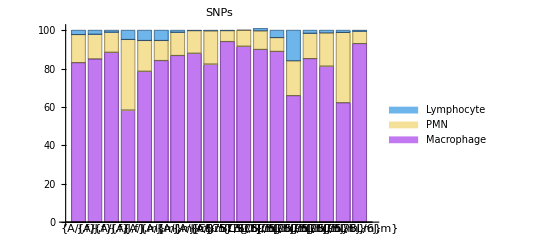

```mathematica
data=Import["/Users/aakritilakshmanan/Downloads/inflamattioncells.csv"];
actualdata=Delete[data,1];
Grid[actualdata,Frame->All];
{strainn,sex,bALmac,bALlym,bALnuet}=Transpose[actualdata];
lables=Transpose[{strainn,sex}];
BarChart[Transpose[{bALmac,bALlym,bALnuet}],ChartLayout->"Stacked", ChartLabels->{lables,None}, ChartStyle->"Pastel",PlotLabel->HoldForm[SNPs],ChartLegends->{"Macrophage","PMN","Lymphocyte"},LabelStyle->{GrayLevel[0]}]
```

This bar chart represents the percentages of different kinds of cells found in the bronchoalveolar lavage of the different strains. Both genders were represented in this data. The presence of these cells allows for scientists to see the different inflammation response of the strains. Both strains had a similar variance in the amount of cells, and there wasn’t a significant difference.

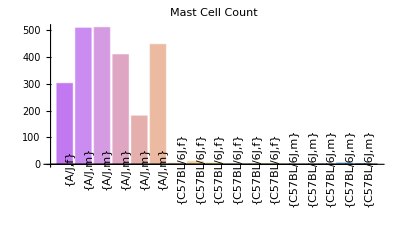

```mathematica
mastdata=Import["/Users/aakritilakshmanan/Downloads/mast.csv"];
actualmastdata=Delete[mastdata,1];
Grid[actualmastdata,Frame->All];
{strainnn,sexx,mast,alveolitis}=Transpose[actualmastdata];
lables=Transpose[{strainnn,sexx}];
BarChart[mast, ChartLabels->Placed[lables,Below,Rotate[#,90 Degree] &], ChartStyle->"Pastel",PlotLabel->HoldForm["Mast Cell Count"],LabelStyle->{GrayLevel[0]}]
BarChart[alveolitis, ChartLabels->Placed[lables,Below,Rotate[#,90 Degree] &], ChartStyle->"Pastel",PlotLabel->HoldForm["Alveolitis Levels"],LabelStyle->{GrayLevel[0]}]
```

This graph describes the amount of mast cells found in each mouse tested. Mast cells are part of the immune system, and the amount present can allow scientists to quantify the inflammation. There was a large difference between the A/J strain and the Black 6 strain. The A/J strain had a much higher count than the other cells. Therefore, there is a variant in the A/J mice that causes this high response.

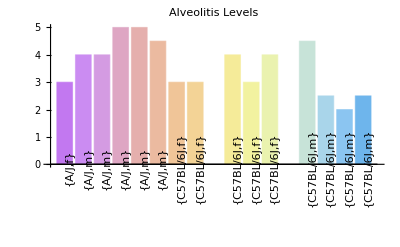

This graph describes the alveolitis levels found in each mouse tested. It was measured on a scale, with 1 being the lowest and 7 being the highest levels. There was a lot of variance in these values as well, but A/J mice generally had higher levels.

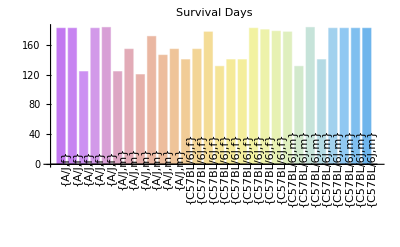

```mathematica
diedata=Import["/Users/aakritilakshmanan/Downloads/fibrosis.csv"];
diemastdata=Delete[diedata,1];
Grid[diemastdata,Frame->All];
{strainnnn,sexxx,survival,x}=Transpose[diemastdata];
labless=Transpose[{strainnnn,sexxx}];
BarChart[survival, ChartLabels->Placed[labless,Below,Rotate[#,90 Degree] &], ChartStyle->"Pastel",PlotLabel->HoldForm["Survival Days"],LabelStyle->{GrayLevel[0]}]
```

This table shows the survival days for the mice, and there was variation between the strains. The B6 mice generally stayed alive the longest.

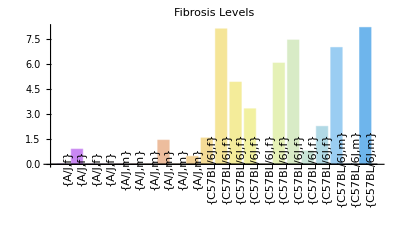

```mathematica
fibrosdata=Import["/Users/aakritilakshmanan/Downloads/fibrssssss.csv"];
newfibrosdata=Delete[fibrosdata,1];
Grid[newfibrosdata,Frame->All];
{strainnnnn,sexxxx,fibrosis}=Transpose[newfibrosdata];
lablesss=Transpose[{strainnnnn,sexxxx}];
BarChart[fibrosis, ChartLabels->Placed[lablesss,Below,Rotate[#,90 Degree] &], ChartStyle->"Pastel",PlotLabel->HoldForm["Fibrosis Levels"],LabelStyle->{GrayLevel[0]}]
```

There is a large difference between the scar tissue amount in the A/J strains and the B6 strains. Due to the fact that the A/J strain mice didn’t display almost any fibrosis, there is probably a variant or SNP in this strain that causes the expression of the gene that results in fibrosis to be reduced. Specifically, the research found that alleles on chromosomes 1/17 caused the A/J mice to be protected from the formation of fibrosis. [9]

I certify that this work was completed by me on February 19, 2020.  All references and resources are cited.  Assistance was provided by NAME OF PERSON(S) (if any)
  Electronic signature: -Graphics-

References:

1.	Labome. (n.d.). Laboratory Mice And Rats. Retrieved February 19, 2020, from https://www.labome.com/method/Laboratory-Mice-and-Rats.html
	2.	(n.d.). 000664 - C57BL/6J. Retrieved February 19, 2020e, from https://www.jax.org/strain/000664
	3.	(n.d.). Cdh23 MGI Mouse Gene Detail - MGI:1890219 - Cadherin 23 (otocadherin). Retrieved February 19, 2020c, from http://www.informatics.jax.org/marker/MGI:1890219
	4.	(n.d.). Cdh23 MGI Mouse Gene Detail - MGI:1890219 - Cadherin 23 (otocadherin). Retrieved February 19, 2020c, from http://www.informatics.jax.org/marker/MGI:1890219
	5.	(n.d.). Genomic Alignments - Mus Musculus - Ensembl Genome Browser 99. Retrieved February 19, 2020b, from http://uswest.ensembl.org/Mus_musculus/Gene/Compara_Alignments?
	6.	 000646 - A/J. https://www.jax.org/strain/000646. Accessed 18 Feb. 2020.
	7.	A/J Strain Detail MGI Mouse MGI:2159747. http://www.informatics.jax.org/strain/MGI:2159747. Accessed 18 Feb. 2020.
	8.	“Retrieval.” Jackson Lab, https://phenome.jax.org/snp/retrieval. Accessed 18 Feb. 2020.
	9.	Paun, A., & Haston, C. K. (2012). Genomic and genome-wide association of susceptibility to radiation-induced fibrotic lung disease in mice.Â Radiotherapy and Oncology,Â 105(3), 350â€“357. Retrieved February 19, 2020, from 10.1016/j.radonc.2012.08.004